# Projeto de Inovação com Algoritmos Genéticos

## Relatório de Disciplina

José Geraldo de Carvalho Pereira

## Análise do problema

### Tamanho da População

O primeiro passo no design de algoritmos genéticos competentes é o cálculo para estimar o tamanho da população. O tamanho da população N pode ser estimado usando a equação (Equação 1) desenvolvida por Harik  et al.(1997), a qual considera dois fatores que influenciam na convergência para uma solução ótima: (1) o suprimento inicial de building blocks (BBs) e a seleção dos melhores BBs em detrimento de seus competidores.

A equação (1) é baseada em um modelo de random walk que representa o suprimento e a competição entre BBs como o Problema da Ruína do Jogador.

N ≥ -2^(k-1)ln(α)(σ_bb √(π(m-1))/d)

Onde k é o tamanho do BB, α é a probabilidade de falha, σ_bb é o desvio padrão do fitness dos BBs, d é a diferença entre o melhor e o segundo melhor BB e m representa o número máximo de BBs. O termo σ_bb √π(m-1) representa a interferência do ruído na competição entre BBs.

Para, por exemplo, assegurar a convergência para uma solução próxima a ótima com uma probabilidade maior que 95%, o α deve ser menor que 5%.

Neste problema temos que k =1, pois cada BB corresponde a um estado dos elementos da regra de transição do autômato celular e m=13248 que são os números desses elementos variáveis na regra de transição. Os parâmetros σ_bb e d foram calculados de 500000 indivíduos gerados aleatoriamente e apresentaram os valores de 0,02399451 e 0,001972661.

```mathematica
sigma = 0.0241745599487;
dist = 0.001972661;
```

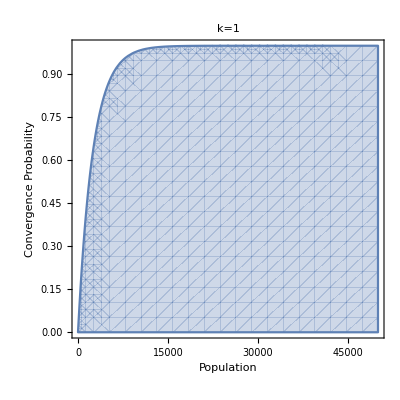

```mathematica
RegionPlot[n ≥-2^(1-1)Log[1-x](sigma√(Pi(13248-1))/dist),{n, 0,50000} , {x,0,1}, FrameLabel-> {"Population", "Convergence Probability"}, PlotLabel->"k=1"]
```

Com um erro (α) de 0.01 (1%) o tamanho estimado da população é de aproximadamente 11.500 indivíduos.

```mathematica
-2^(1-1)Log[0.01](sigma √(Pi(13248-1)))/dist
```

11512.9

No entanto, essa equação foi desenvolvida para algoritmos genéticos com representação binária e o nosso problema apresenta 4 estados possíveis para cada elemento da regra de transição dos autômatos. Dessa forma, talvez seja necessário considerar k = 2, o que no GA binário representa 4 possibilidades. Portanto, poderíamos considerar que no nosso problema, k=2 está implícito na codificação.

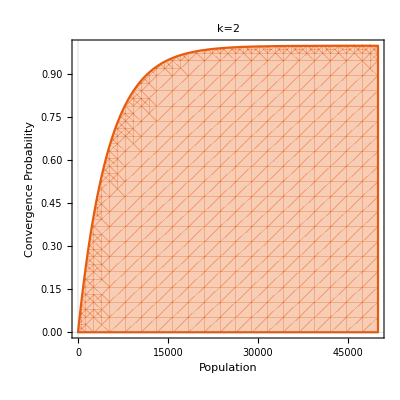

```mathematica
RegionPlot[n≥-(2^(2-1) Log[1-x] (sigma √(Pi(13248-1))))/dist,{n,0,50000},{x,0,1},PlotTheme->"Scientific",FrameLabel-> {"Population", "Convergence Probability"}, PlotLabel->"k=2"]
```

Para k=2 e erro (α) de 0.01 (1%) o tamanho estimato da população é de aproximadamente 23000 indivíduos.

```mathematica
-2^(2-1)Log[0.01](sigma √(Pi(13248-1)))/dist
```

23025.8

### Complexidade computacional

Após a estimação do tamanho da população, podemos analisar a complexidade do GA. A complexidade é medida como o número de funções necessárias para atingir a solução ótima e pode ser calculada como o número de gerações, ou tempo de convergência, multiplicado pelo tamanho da população.

O tempo de convergência é afetado pela taxa relativa com que os genes convergem. Por exemplo, quando todos os genes são igualmente importantes para a solução e a convergência ocorre uniformemente, o tempo de convergência é  uma função de O(√l), onde l é o tamanho da string de genes. Quando a importância de cada gene varia, a convergência ocorre sequencialmente e consequentemente, o tempo de convergência é uma função de O(l). Esses dois casos representam o limite inferior e superior da complexidade do tempo de convergência.

Assumindo uma seleção por torneio, Thierens e Goldberg (1994) e Thierens e colaboradores (1998), demonstraram que o tempo de convergência para todas as strings, assumindo uma convergência sequencial dos genes é:

t = 2l

Assim, podemos estimar um tempo de convergência colocando um limite superior calculado pela equação 2. Considerando l = 13248 temos que o o tempo de convergência será de 26496 gerações. Entretanto, como mencionado anteriormente, cada gene tem 4 estados possíveis e teoria foi desenvolvida para genes com apenas dois estados (binários). Com isso, pode ser necessário considerar l = 2 * 13248, uma vez que l = k m  e poderiamos considerar k = 2. Isso resultaria em um t = 53000

```mathematica
t = 2*13248
```

26496

ou, se k = 2

```mathematica
t = 2*2*13248
```

52992

### Análise da deriva genética

A deriva genética ocorre em uma população quando a mutação e o crossover fazem os genes flutuarem e convergirem para um solução não ótima na ausência de uma pressão seletiva.

O número experado de gerações para os genes convergirem na ausência de pressão seletiva para uma população inicial de strings binárias geradas randomicamente com proporções iguais de 0s e 1s (Thierens et al., 1998) é estimado como:

t_drift= 1.4N

O que no nosso caso resulta em:

```mathematica
tdrift = 1.4 11500
```

16100.

para k =1 e

```mathematica
tdrift = 1.4 23000
```

32200.

para k=2.

A equação 3 mostra que o tempo de convergência devido a deriva genética é uma função linear do tamanho da população. Para assegurar que uma ocorra uma  convergência para um ótimo ao invés de uma convergência por deriva genética podemos satisfazer a condição

t < t_drift

No nosso problema, tanto considerando k = 1 como considerando k = 2, a inequação não é satisfeita. Consequentemente, pode ser necessário aumentar o N em ambos os casos. Para k = 1 podemos aumentar N para aproximadamente 19000 ou mais, e para k = 2, podemos aumentar N para 38000 ou mais, assim, conseguimos satisfazer a inequação.

```mathematica
26496/1.4
```

18925.7

```mathematica
52992/1.4
```

37851.4

### Conclusão

O design de algoritmos genéticos competentes reduz o tempo gasto na busca por parâmetros que resultem em soluções ótimas ou quase-ótimas. No nosso caso, conseguimos estimar alguns  parâmetros como o tamanho da população igual de aproximadamente 20000 (ou 40000 caso k = 2) e um número gerações de 25000 (ou 50000 caso k=2). Entretanto, apesar de acreditarmos serem parâmetros viáveis, o atual estado do programa impossibilita tais testes no momento. Acreditamos que algumas otimizações e uma melhora da paralelização permitirá tais testes.